## Hexi—PS15—2025 - 04 - 01

### Exercises from EIWL3 Section 37

```mathematica
Table[Style[n,Background->If[EvenQ[n],Yellow,LightGray]],{n,100}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Table[If[PrimeQ[n],Framed[n],n],{n,100}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Table[If[PrimeQ[n],Labeled[Framed[n],Style[Mod[n,4],LightGray]],n],{n,100}]
```

{1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100}

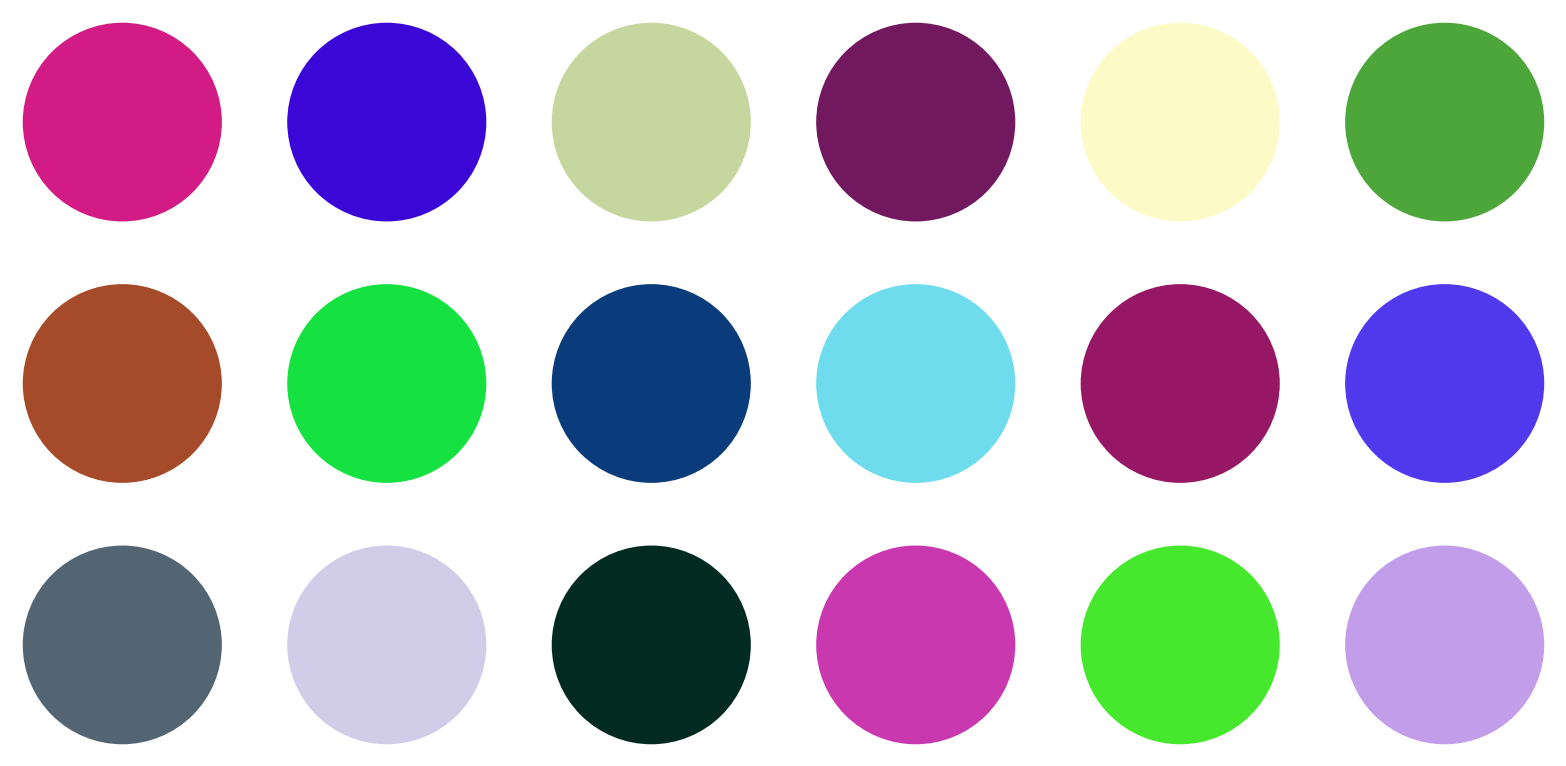

```mathematica
GraphicsGrid[Table[Graphics[{RandomColor[],Disk[]}],3,6]]
```

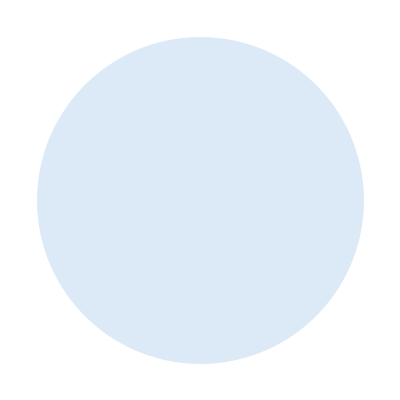

```mathematica
PieChart[]
```

-Graphics-

```mathematica
PieChart[EntityClass["Country","GroupOf5"]["GDP"],ChartLabels->EntityClass["Country","GroupOf5"]["Name"]]
```

-Graphics-

```mathematica
PieChart[EntityClass["Country","GroupOf5"]["Population"],ChartLegends->EntityClass["Country","GroupOf5"]["Name"]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[PieChart[Values[Counts[IntegerDigits[2^n]]]],{n,1,25}],5]]
```

-Graphics-

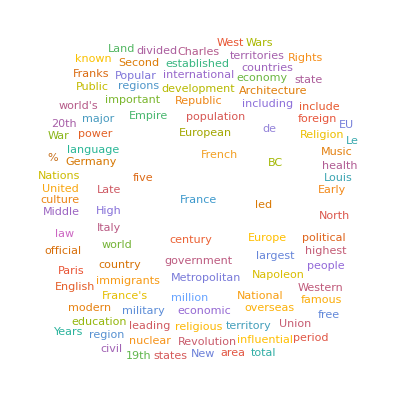
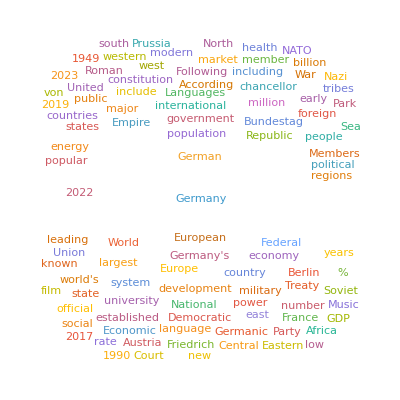
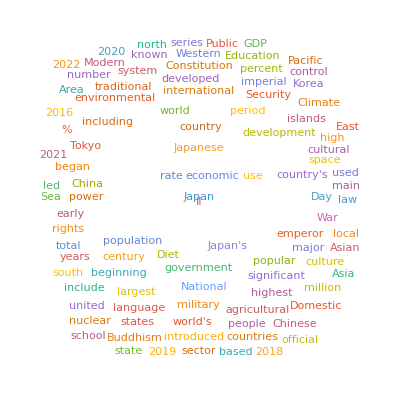
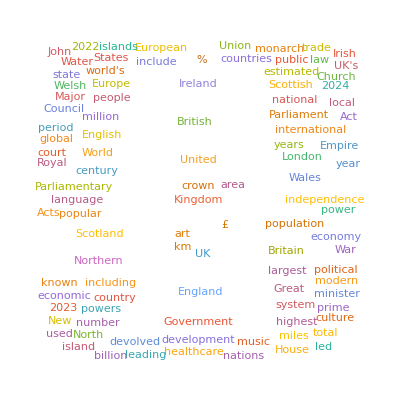
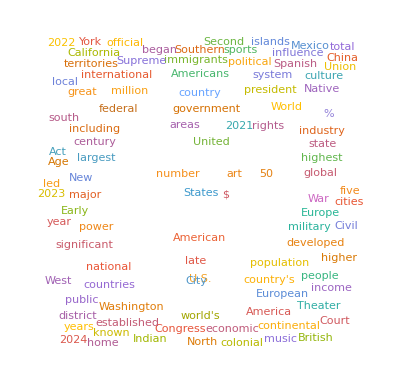

```mathematica
WordCloud[WikipediaData[#]]&/@EntityClass["Country","GroupOf5"]["Name"]
```

### Exercises from EIWL3 Section 38

```mathematica
Module[{x=Range[10]},x^2+x]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
Module[{x=Table[RandomInteger[100],10]},Column[{x,Sort[x],Max[x],Total[x]}]]
```

{18,83,9,91,1,69,37,33,81,25}
{1,9,18,25,33,37,69,81,83,91}
91
447

```mathematica
Module[{x=EntityValue[Entity["TaxonomicSpecies","GiraffaCamelopardalis::y5488"],"Image"]},{Blur[x],EdgeDetect[x],ColorNegate[x]}]
```

{-Graphics-,-Graphics-,-Graphics-}

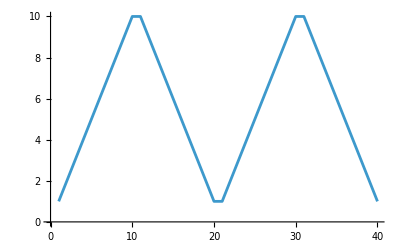

```mathematica
Module[{r=Range[10]},ListLinePlot[Join[r,Reverse[r],r,Reverse[r]]]]
```

```mathematica
Module[{r=Range[10]},{r+1,r-1,Reverse[r]}]
```

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

```mathematica
NestList[Mod[17#+2,11]&,10,20]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

```mathematica
vowels={"a","e","i","o","u"};
lv=LetterNumber[#]&/@{"a","e","i","o","u"};
consonants=Delete[Delete[Delete[Delete[Delete[Alphabet[],lv[[1]]],lv[[2]]],lv[[3]]],lv[[4]]],lv[[5]]];
Module[{c=consonants,v=vowels},Table[StringJoin[RandomSample[c,1],RandomSample[v,1],RandomSample[c,1],RandomSample[v,1],RandomSample[c,1]],10]]
```

{cajox,bamun,xecap,puqaj,vaoot,qenaw,duxet,xieie,gevap,eoqit}